# Proyecto 1: Modelo de Lotka-Volterra

Es el año 2021, y la pandemia del Covid-19 ha mutado y ahora tiene la capacidad de convertir en zombies viajeros a las personas infectadas. Se espera que para dentro de unos años ya habrá una cura desarrollada para que las personas infectadas regresen a la normalidad, pero mientras tanto hay que mantener viva a la especie humana y a los infectados.

Un modelo para describir la evolución de la población de humanos y zombies infectados está dado por las ecuaciones de Lotka-Volterra:

donde x representa la población sana, y la población enferma, α la tasa de crecimiento de la población sana, β la tasa de mortalidad de la población sana debido al virus, δ la tasa de crecimiento de la población infectada y γ es la tasa de mortalidad de las personas infectadas.

Durante el transcurso de la epidemia se hace la observación de que la tasa de reproducción del virus es afectada por la temperatura, haciendo que se reproduzca más rápido en épocas frías y más lento en épocas cálidas. El efecto estacional se puede modelar añadiendo un término proporcional a Sin(t) a las ecuaciones diferenciales que modelan la población:

x’(t) = α x(t) - β x(t) y(t),
y’(t) = δ x(t) y(t)- γ y(t)+σ Sin(t),

donde σ es un coeficiente que representa qué tanto afecta el elemento estacional. Supongamos en este proyecto que σ = 0.1.
En la figura se muestra un ejemplo de la evolución de las poblaciones:

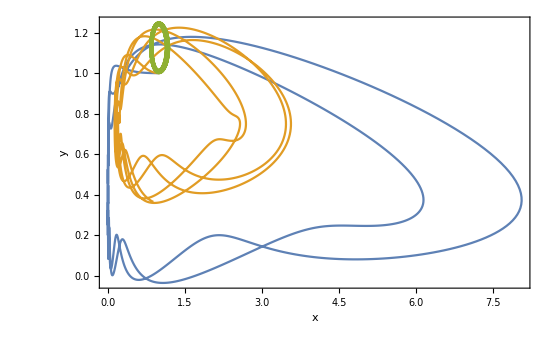

Supongamos que se normaliza la población de personas sanas e infectados para que inicialmente x(0) = 1 ,  y(0) = 1, y la tasa de reproducción y muerte del virus es γ = δ = 0.1. Se desea encontrar una manera de mantener ambas poblaciones estables hasta que se encuentre una cura para el virus.

El proyecto consiste en encontrar una combinación de parámetros α y β que produzcan órbitas estables. Crear una manipulación interactiva donde se puedan cambiar las poblaciones iniciales y los parámetros α, β, γ, δ.